```mathematica
SetDirectory[NotebookDirectory[]];
```

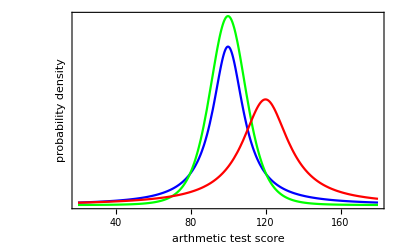

```mathematica
μ = 100;
σ1 = 10;
ν1 = 1;
ν2= 5;
σ2 = 15;
g4=Plot[{PDF[StudentTDistribution[μ,σ1,ν1],x],PDF[StudentTDistribution[μ,σ1,ν2],x],PDF[StudentTDistribution[120,σ2,ν1],x]},{x,20,180},PlotRange->Full,Frame->{True,True,False,False},BaseStyle->Medium,FrameLabel->{"arthmetic test score","probability density"},Axes->{False,False},FrameTicks->{True,False},PlotStyle->{Blue,Green,Red}]
```

```mathematica
Export["Distributions_tArithmeticDistributionExposition.pdf",g4]
```

Distributions_tArithmeticDistributionExposition.pdf

```mathematica
data = RandomVariate[StudentTDistribution[μ,σ1,ν1],{5}];
```

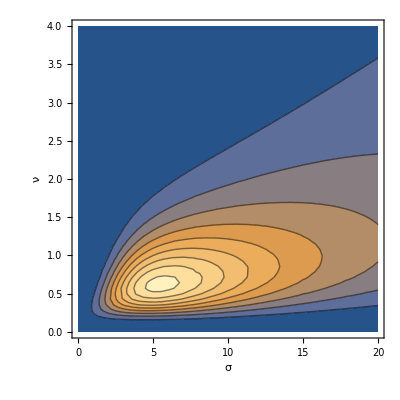

```mathematica
g1=ContourPlot[Likelihood[StudentTDistribution[100,σ,ν],data],{σ,0,20},{ν,0,4},PlotRange->Full,Frame->{True,True,False,False},FrameLabel->{"σ","ν"},BaseStyle->Medium]
```

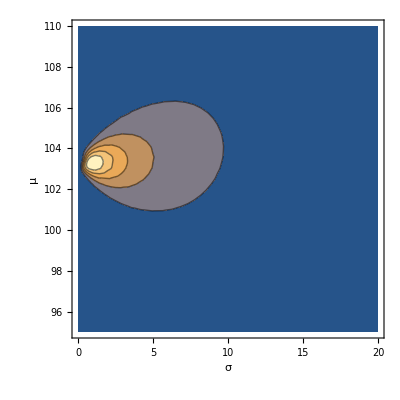

```mathematica
g2=ContourPlot[Likelihood[StudentTDistribution[μ,σ,ν1],data],{σ,0,20},{μ,95,110},PlotRange->Full,Frame->{True,True,False,False},FrameLabel->{"σ","μ"},BaseStyle->Medium]
```

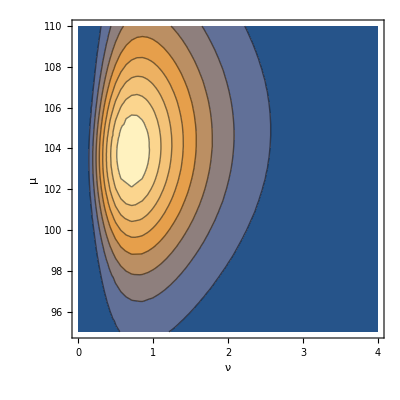

```mathematica
g3=ContourPlot[Likelihood[StudentTDistribution[μ,σ1,ν],data],{ν,0,4},{μ,95,110},PlotRange->Full,Frame->{True,True,False,False},FrameLabel->{"ν","μ"},BaseStyle->Medium]
```

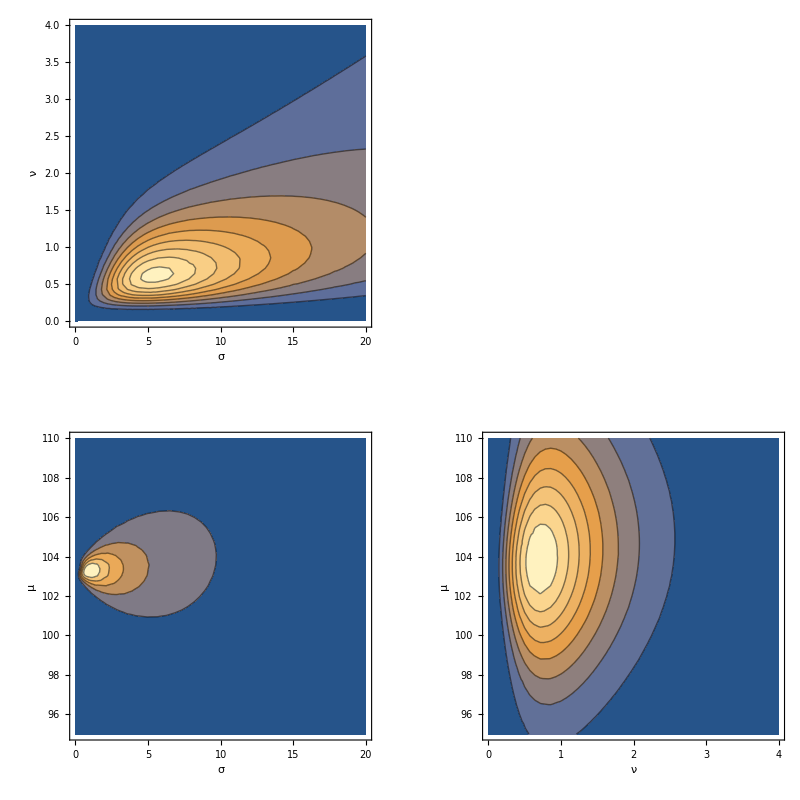

```mathematica
Show[GraphicsGrid[{{g1,},{g2,g3}}],ImageSize->800]
```